```mathematica
P1=Plot3D[{z=Sqrt[2x]},{x,0,3},{y,-2,2},Axes->False, BoxRatios->{4,4,4},PlotStyle->{Green,Opacity[0.9]},Mesh->0,PlotPoints->100];
P2=Plot3D[{z=-Sqrt[2x]},{x,0,3},{y,-2,2},Axes->False, BoxRatios->{3,4,2Sqrt[6]},PlotStyle->{Green,Opacity[0.9]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{r*Cos[theta],r*Sin[theta],r},{theta,0,2Pi},{r,0,3},Axes->False, BoxRatios->{3,3,3},PlotStyle->{Yellow,Opacity[0.9]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-4,0,0},{4,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-4},{0,0,4}}]},{Black,Arrowheads[.03],Arrow[{{0,-4,0},{0,4,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
(*,Text[Style["y",FontSize->18,FontFamily->"Times New Roman",FontSlant->Italic],{0,4,-0.1}]*)
Show[G1,P1,P2,P3,ViewPoint->{0,0,+Infinity},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{r*Cos[theta],r*Sin[theta],1/2*r^2},{theta,0,2Pi},{r,0,1.2},Axes->False, BoxRatios->{1,1,1.44/2},PlotStyle->{Yellow,Opacity[0.9]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{1*Cos[theta],1*Sin[theta],z},{theta,0,2Pi},{z,-1,1},Axes->False, BoxRatios->{1,1,2},PlotStyle->{Green,Opacity[0.4]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.8,0,0},{1.8,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.8},{0,0,1.8}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.8,0},{0,1.8,0}}]}},Axes->False,BoxRatios->{1.8,1.8,1.8}];
Show[G1,P1,P2,ViewPoint->{0,0,+Infinity},Boxed->False]
```

-Graphics3D-

```mathematica
P2=ParametricPlot3D[{1*Cos[theta],1*Sin[theta],z},{theta,0,2Pi},{z,-1,1},Axes->False, BoxRatios->{1,1,2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
P1=Plot3D[{x*y},{x,-1.2,1.2},{y,-1.2,1.2},Axes->False, BoxRatios->{1.2,1.2,1.44},PlotStyle->{Yellow,Opacity[0.9]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.8,0,0},{1.8,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.8},{0,0,1.8}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.8,0},{0,1.8,0}}]}},Axes->False,BoxRatios->{1.8,1.8,1.8}];
Show[G1,P1,P2,ViewPoint->{0,0,+Infinity},Boxed->False]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{Sin[phi]*Cos[theta],Sin[phi]Sin[theta],1Cos[phi]},{theta,-Pi/2,Pi/2},{phi,0,Pi},Axes->False, BoxRatios->{1,1,1.44/2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,BoxRatios->{1.5,1.5,1.5}];
Show[G1,P1,ViewPoint->{2,0,0},Boxed->False]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{r*Cos[theta],r*Sin[theta],r^2},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{r*Cos[theta],r*Sin[theta],0},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Gray,Opacity[0.5]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,BoxRatios->{1.5,1.5,1.5}];
Show[G1,P1,P2,ViewPoint->{0,0,2},Boxed->False]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{Sin[phi]*Cos[theta],Sin[phi]Sin[theta],1Cos[phi]},{theta,0,2Pi},{phi,0,Pi},Axes->False, BoxRatios->{1,1,1.44/2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,BoxRatios->{1.5,1.5,1.5}];
Show[G1,P1,ViewPoint->{2,2,1},Boxed->False]
```

-Graphics3D-

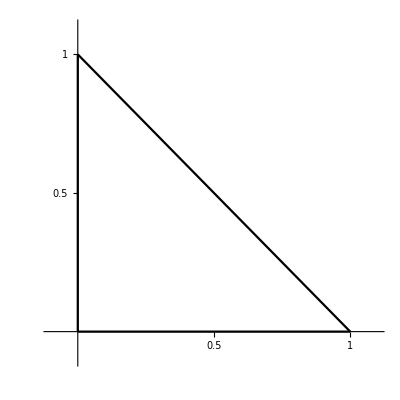

```mathematica
f[x_]:=1-x;g[x_]:=1/2-x;
Quxian1=Plot[f[x],{x,0,1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
Quxian2=Plot[0,{x,0,1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
LX0=ParametricPlot[{0,y},{y,0,1},PlotStyle->Black,PlotStyle->Black];
Show[Quxian1,Quxian2,LX0,PlotRange->{{-0.1,1.1},{-0.1,1.1}}]
```

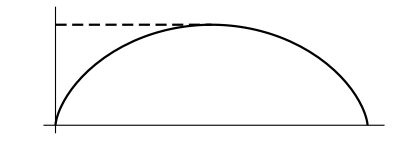

```mathematica
LX0=ParametricPlot[{t-Sin[t],1-Cos[t]},{t,0,2Pi},AxesStyle->Arrowheads[0.04],PlotStyle->Black,Ticks->None];
LX1=Plot[{2},{t,0,Pi},AxesStyle->Arrowheads[0.04],PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]},Ticks->None];
Show[LX0,LX1,PlotRange->{{-0.1,2Pi+0.2},{-0.1,2.3}},AspectRatio->2.4/(2Pi+0.3)]
```

```mathematica
P1=ParametricPlot3D[{Exp[-t]Cos[t],Exp[-t]Sin[t],Exp[-t]},{t,0,1000},Axes->False, BoxRatios->{1,1,1.44/2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,BoxRatios->{1.5,1.5,1.5}];
Show[G1,P1,ViewPoint->{0,-Infinity,0},Boxed->False]
```

-Graphics3D-

```mathematica
P1=ParametricPlot3D[{1Cos[t],1Sin[t],0.2t},{t,0,2Pi},Axes->False, BoxRatios->{1,1,1.44/2},PlotStyle->{Green,Opacity[0.5]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,BoxRatios->{1.5,1.5,1.5}];
Show[G1,P1,Boxed->False]
```

-Graphics3D-

```mathematica
P1=Plot3D[{z=Sqrt[1-x^2-y^2]},{x,-1,1},{y,-1,1}, BoxRatios->{4,4,4},PlotStyle->{Green,Opacity[0.6]},Mesh->0,PlotPoints->100];
P2=Plot3D[{z=-Sqrt[1-x^2-y^2]},{x,-1,1},{y,-1,1},BoxRatios->{3,4,2Sqrt[6]},PlotStyle->{Green,Opacity[0.6]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{Cos[theta]*Cos[theta],Cos[theta]*Sin[theta],z},{theta,0,2Pi},{z,-1.2,1.2},AspectRatio->2,PlotStyle->{Yellow,Opacity[0.6]},Mesh->0,PlotPoints->100];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},AxesOrigin->{0,0,0},AxesLabel->CharacterRange["X","Z"]];
Show[G1,P1,P2,P3,ViewPoint->{0.5,1,1},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-